Task1

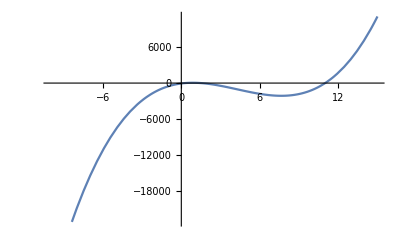

x1 = 10.999, число шагов: 11

289

x1 = 11, x2 = 3/2, x3 = 2/7

Task2

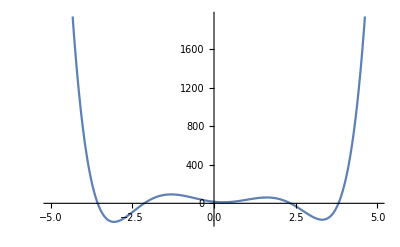

{{x→-3.55796},{x→-2.13385},{x→0.273421-0.402557 ⅈ},{x→0.273421+0.402557 ⅈ},{x→2.337},{x→3.80797}}

Task3

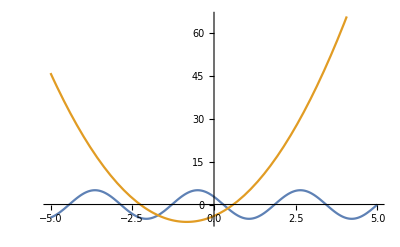

{x→0.422388}

{x→-1.71202}

```mathematica
"Task1"
f[x_] := 14 x^3-179 x^2+281x-66
Plot[f[x],{x,-10,15}, AxesOrigin->{0,0}]
eps = 0.001; l = 9; k =11;
Do[x1=(l+k)/2.;
fx1= f[x1];
If[f[l]*fx1 < 0, k =x1, If[fx1 != 0, l= x1]];
If[Abs[k-l]<eps||fx1== 0,
Print["x1 = ", x1//N, ", число шагов: ", n];
Break[]],
{n,1,100}
]
g[x_] =14 x^2-25x+6;
b = -25;a = 14;c = 6;
d= b*b -4*a*c
x2 = (-b + √d)/(2*a);
x3 = (-b - √d)/(2*a);
Print ["x1 = ",Round[x1], ", x2 = ", x2, ", x3 = ", x3];
"Task2"
f2[x_]:= x^6-x^5-18 x^4+14 x^3+61 x^2-36x+16
Plot[f2[x], {x,-5,5}]
NSolve[f2[x] == 0, x]
"Task3"
f3[x_]:= 5*Cos[2x+1];
g3[x_]:=3 x^2+5x-4;
Plot[{f3[x],g3[x]},{x,-5,5}]
FindRoot[f3[x]==g3[x], {x,0.5}]
FindRoot[f3[x]==g3[x], {x,-2}]
```